```mathematica
Clear["Global`*"]
```

# The limit of vanishing radial drifts

## For the available energy of curvature-driven ions

R.J.J. Mackenbach

EPFL-SPC

## The constraint on the density

### Integral over the parallel velocity

We require the following integral

```mathematica
ℐnegative=1/(√π)*Integrate[Exp[-x]/(√x)*(x-x0),{x,0,∞}]
ℐleft=1/(√π)*Integrate[Exp[-x]/(√x)*(x0-x),{x,0,x0},Assumptions->x0>0]
ℐright=1/(√π)*Integrate[Exp[-x]/(√x)*(x-x0),{x,x0,∞},Assumptions->x0>0]
ℐpositive=FullSimplify[ℐleft+ℐright-ℐnegative]
```

1/2 (1-2 x0)

(ⅇ^-x0 √x0+1/2 √π (-1+2 x0) Erf[√x0])/(√π)

(ⅇ^-x0 √x0-1/2 √π (-1+2 x0) Erfc[√x0])/(√π)

(2 ⅇ^-x0 √x0)/(√π)+(-1+2 x0) Erf[√x0]

This may the equivalently be written as

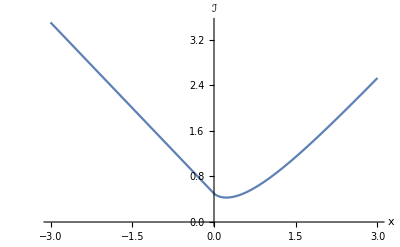

```mathematica
ℐ[x0_]:=1/2 (1-2 x0)+HeavisideTheta[x0]*((2 ⅇ^-x0 √x0)/(√π)+(-1+2 x0) Erf[√x0])
Plot[ℐ[x],{x,-3,3},PlotRange->{0,ℐ[-3]},AxesLabel->{"x","ℐ"}]
```

### Integral over the perpendicular velocity

We now require the integral over perpendicular velocity. It may be written as

```mathematica
ℋnegative=FullSimplify[Integrate[b^2*Exp[-x0*b]*ℐ[x0],{x0,0,x}, Assumptions->x<0]]
ℋpositive=FullSimplify[Integrate[b^2*Exp[-x0*b]*ℐ[x0],{x0,0,x}, Assumptions->x>0,GenerateConditions->False]-ℋnegative]
```

1/2 (-2+b+ⅇ^(-b x) (2+b (-1+2 x)))

-(2 b ⅇ^(-((1+b) x)) √x)/(√π)+ⅇ^(-b x) (-2+b-2 b x) Erf[√x]+(2 Erf[√((1+b) x)])/(√(1+b))

This can equivalently be written as

```mathematica
ℋ=ℋnegative+HeavisideTheta[x]*ℋpositive
```

1/2 (-2+b+ⅇ^(-b x) (2+b (-1+2 x)))+(-(2 b ⅇ^(-((1+b) x)) √x)/(√π)+ⅇ^(-b x) (-2+b-2 b x) Erf[√x]+(2 Erf[√((1+b) x)])/(√(1+b))) HeavisideTheta[x]

```mathematica
Plot3D[ℋ,{x,-2,2},{b,-2,2},AxesLabel->{"v_0^2","b","ℋ"}]
```

-Graphics3D-

Let us compare this against numerically evaluating the integral, as a sanity check.

```mathematica
ℋnum[x_,b_]:=NIntegrate[b^2*Exp[-b*y]*ℐ[y],{y,0,x}]
```

Plot the difference

```mathematica
Plot3D[Abs[ℋ-ℋnum[x,b]],{x,-2,2},{b,-2,2},PlotRange->Full]
```

-Graphics3D-

#### Limits of interest

We investigate (2 Erf[√(1+b) √x])/(√(1+b)) term, as it has interesting limits that need to be hard-coded.

```mathematica
FullSimplify[(2 Erf[√(1+b) √x])/(√(1+b))/.{b->-1-c}]/.{c->-1-b}
```

(2 Erfi[√(-1-b) √x])/(√(-1-b))

```mathematica
Limit[(2 Erf[√(1+b) √x])/(√(1+b)),b->-1]
```

(4 √x)/(√π)

Next we evaluate ℋ in the limit of v_⊥->∞, which correspond to v_(||)->σ(b)×∞.

```mathematica
ℋinfneg=Limit[ℋ,x->∞,Assumptions->b>0]
ℋinfpos=Limit[ℋ,x->-∞,Assumptions->b<0]
ℋinf=-1+b/2+(2*HeavisideTheta[b])/(√(1+b))
```

-1+b/2+2/(√(1+b))

1/2 (-2+b)

-1+b/2+(2 HeavisideTheta[b])/(√(1+b))

Finally evaluate ℋ at  v_⊥=0

```mathematica
ℋvperp0=ℋ/.{x->a/b}
```

1/2 (-2+b+(2+(-1+(2 a)/b) b) ⅇ^-a)+(-(2 √(a/b) b ⅇ^(-(a (1+b))/b))/(√π)+(-2-2 a+b) ⅇ^-a Erf[√(a/b)]+(2 Erf[√((a (1+b))/b)])/(√(1+b))) HeavisideTheta[a/b]

#### The right-hand side of the equation

We have found that the right hand side can be written (up to signs) as

```mathematica
RHS=(1/η-ηB/η)*b*Exp[-a]
Eq=(a/b==3/2-1/η)&&(1/b==ηB/η-1)
subs=Solve[Eq,{η,ηB}][[1]]
RHSFinal=FullSimplify[(RHS/.subs)]
```

b ⅇ^-a (1/η-ηB/η)

a/b==3/2-1/η&&1/b==-1+ηB/η

{η→(2 b)/(-2 a+3 b),ηB→(2 (1+b))/(-2 a+3 b)}

1/2 (-2-2 a+b) ⅇ^-a

#### Numerical implementation

To circumvent overflow errors, it is useful to instead write (ℋ(ln(y),b))/b.

```mathematica
Loggedℋ=FullSimplify[ℋ/.{x->Log[y]}]
```

1/2 (-2+b+y^-b (2-b+2 b Log[y]))+HeavisideTheta[Log[y]] ((2 Erf[√((1+b) Log[y])])/(√(1+b))+y^-b (-(2 b √Log[y])/(√π y)+Erf[√Log[y]] (-2+b-2 b Log[y])))

```mathematica
Loggedℋneg=FullSimplify[Loggedℋ,Assumptions->{Log[y]<0}]
LoggedℋHeavi=FullSimplify[FullSimplify[Loggedℋ,Assumptions->{Log[y]>0}]-Loggedℋneg]
```

1/2 (-2+b+y^-b (2-b+2 b Log[y]))

(2 Erf[√((1+b) Log[y])])/(√(1+b))+y^-b (-(2 b √Log[y])/(√π y)+Erf[√Log[y]] (-2+b-2 b Log[y]))

Finally, we Fortranform it for python implementation

```mathematica
FortranForm[Loggedℋneg]
```

(-2 + b + (2 - b + 2*b*Log(y))/y**b)/2.

```mathematica
FortranForm[LoggedℋHeavi]
```

(2*Erf(Sqrt((1 + b)*Log(y))))/Sqrt(1 + b) + ((-2*b*Sqrt(Log(y)))/(Sqrt(Pi)*y) + Erf(Sqrt(Log(y)))*(-2 + b - 2*b*Log(y)))/y**b

## The available energy

### Integral over the parallel velocity

Here we perform the integral over parallel velocity, which is of the form

```mathematica
𝒥integrand=1/(√π)*Exp[-x]/(√x)*Ramp[Ω*(x-x0)]
```

(ⅇ^-x Ramp[(x-x0) Ω])/(√π √x)

Under the condition that x0<0, we may write

```mathematica
𝒥neg=Integrate[Ramp[Ω]/(√π)*Exp[-x]/(√x)*(x-x0),{x,0,∞}]
```

1/2 (1-2 x0) Ramp[Ω]

However if x0>0 we split it up:

```mathematica
𝒥pos1=FullSimplify[Integrate[Ramp[-Ω]/(√π)*Exp[-x]/(√x)*(x0-x),{x,0,x0},Assumptions->x0>0]]
𝒥pos2=FullSimplify[Integrate[Ramp[Ω]/(√π)*Exp[-x]/(√x)*(x-x0),{x,x0,∞},Assumptions->x0>0]]
𝒥pos=FullSimplify[(𝒥pos1+𝒥pos2)/.{Ramp[-Ω]->A[Ω]-Ramp[Ω]}]
Collect[𝒥pos,A[Ω]]
```

1/2 ((2 ⅇ^-x0 √x0)/(√π)+(-1+2 x0) Erf[√x0]) Ramp[-Ω]

1/2 ((2 ⅇ^-x0 √x0)/(√π)+(1-2 x0) Erfc[√x0]) Ramp[Ω]

(ⅇ^-x0 √x0 A[Ω])/(√π)+1/2 (-1+2 x0) (A[Ω] Erf[√x0]-Ramp[Ω])

A[Ω] ((ⅇ^-x0 √x0)/(√π)+1/2 (-1+2 x0) Erf[√x0])-1/2 (-1+2 x0) Ramp[Ω]